## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=0.3; Q=0.8;
```

```mathematica
winit=(0.2-0.00005*I)
```

0.2-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.180297-3.50604×10^-7 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.15

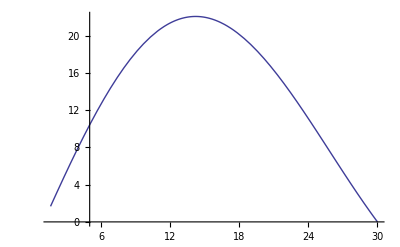

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<151,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,150}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,150}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,-3.50705×10^-7},{30.2,-3.30492×10^-7},{30.4,-3.1144×10^-7},{30.6,-2.93483×10^-7},{30.8,-2.76537×10^-7},{31.,-2.60572×10^-7},{31.2,-2.455×10^-7},{31.4,-2.31278×10^-7},{31.6,-2.17832×10^-7},{31.8,-2.05168×10^-7},{32.,-1.93194×10^-7},{32.2,-1.81889×10^-7},{32.4,-1.7121×10^-7},{32.6,-1.61151×10^-7},{32.8,-1.51595×10^-7},{33.,-1.42585×10^-7},{33.2,-1.34066×10^-7},{33.4,-1.26017×10^-7},{33.6,-1.18407×10^-7},{33.8,-1.1121×10^-7},{34.,-1.04392×10^-7},{34.2,-9.7954×10^-8},{34.4,-9.18742×10^-8},{34.6,-8.60897×10^-8},{34.8,-8.06418×10^-8},{35.,-7.54809×10^-8},{35.2,-7.05882×10^-8},{35.4,-6.59762×10^-8},{35.6,-6.1591×10^-8},{35.8,-5.74586×10^-8},{36.,-5.35426×10^-8},{36.2,-4.98232×10^-8},{36.4,-4.63134×10^-8},{36.6,-4.29926×10^-8},{36.8,-3.98423×10^-8},{37.,-3.68683×10^-8},{37.2,-3.40479×10^-8},{37.4,-3.13853×10^-8},{37.6,-2.88607×10^-8},{37.8,-2.64661×10^-8},{38.,-2.42067×10^-8},{38.2,-2.20659×10^-8},{38.4,-2.0044×10^-8},{38.6,-1.81304×10^-8},{38.8,-1.63178×10^-8},{39.,-1.46063×10^-8},{39.2,-1.29871×10^-8},{39.4,-1.14545×10^-8},{39.6,-1.00092×10^-8},{39.8,-8.64162×10^-9},{40.,-7.34946×10^-9},{40.2,-6.11494×10^-9},{40.4,-4.9759×10^-9},{40.6,-3.88967×10^-9},{40.8,-2.86186×10^-9},{41.,-1.89369×10^-9},{41.2,-9.79802×10^-10},{41.4,-1.19463×10^-10},{41.6,6.91454×10^-10},{41.8,1.45519×10^-9},{42.,2.17384×10^-9},{42.2,2.84964×10^-9},{42.4,3.48708×10^-9},{42.6,4.08454×10^-9},{42.8,4.64593×10^-9},{43.,5.17343×10^-9},{43.2,5.66656×10^-9},{43.4,6.12875×10^-9},{43.6,6.56099×10^-9},{43.8,6.96724×10^-9},{44.,7.34535×10^-9},{44.2,7.69838×10^-9},{44.4,8.02664×10^-9},{44.6,8.32557×10^-9},{44.8,8.61632×10^-9},{45.,8.87974×10^-9},{45.2,9.13073×10^-9},{45.4,9.34778×10^-9},{45.6,9.55438×10^-9},{45.8,9.74726×10^-9},{46.,9.92225×10^-9},{46.2,1.0081×10^-8},{46.4,1.02278×10^-8},{46.6,1.03318×10^-8},{46.8,1.04807×10^-8},{47.,1.0587×10^-8},{47.2,1.06822×10^-8},{47.4,1.07667×10^-8},{47.6,1.08582×10^-8},{47.8,1.08918×10^-8},{48.,1.09606×10^-8},{48.2,1.10068×10^-8},{48.4,1.10451×10^-8},{48.6,1.10926×10^-8},{48.8,1.1098×10^-8},{49.,1.11141×10^-8},{49.2,1.11206×10^-8},{49.4,1.11256×10^-8},{49.6,1.11224×10^-8},{49.8,1.11137×10^-8},{50.,1.1097×10^-8},{50.2,1.10806×10^-8},{50.4,1.1057×10^-8},{50.6,1.10288×10^-8},{50.8,1.09973×10^-8},{51.,1.09604×10^-8},{51.2,1.09205×10^-8},{51.4,1.08773×10^-8},{51.6,1.08308×10^-8},{51.8,1.07812×10^-8},{52.,1.0729×10^-8},{52.2,1.06738×10^-8},{52.4,1.06166×10^-8},{52.6,1.05566×10^-8},{52.8,1.04909×10^-8},{53.,1.04309×10^-8},{53.2,1.03574×10^-8},{53.4,1.02977×10^-8},{53.6,1.02285×10^-8},{53.8,1.01581×10^-8},{54.,1.00863×10^-8},{54.2,1.00131×10^-8},{54.4,9.93944×10^-9},{54.6,9.86376×10^-9},{54.8,9.79179×10^-9},{55.,9.70151×10^-9},{55.2,9.63182×10^-9},{55.4,9.55456×10^-9},{55.6,9.47568×10^-9},{55.8,9.39632×10^-9},{56.,9.31621×10^-9},{56.2,9.2359×10^-9},{56.4,9.15531×10^-9},{56.6,9.07444×10^-9},{56.8,8.99235×10^-9},{57.,8.91219×10^-9},{57.2,8.83126×10^-9},{57.4,8.74857×10^-9},{57.6,8.66829×10^-9},{57.8,8.58683×10^-9},{58.,8.50562×10^-9},{58.2,8.4246×10^-9},{58.4,8.34355×10^-9},{58.6,8.26303×10^-9},{58.8,8.18229×10^-9},{59.,8.10207×10^-9},{59.2,8.02206×10^-9},{59.4,7.94236×10^-9},{59.6,7.85408×10^-9},{59.8,7.78402×10^-9},{60.,7.70511×10^-9}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*The imaginary part vs the radius*)
```

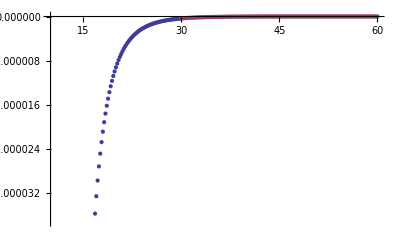

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

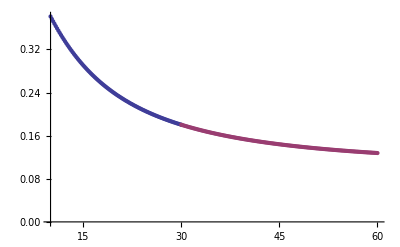

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.80/q=0.3/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.80/q=0.3/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.80/q=0.3/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.80/q=0.3/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```